```mathematica
Needs["FindBounce`"]
```

Multiple Scalar Field (if function is given)

We define a two field potential V with known minima locations and calculate its bounce configuration. Option “MidFieldPoint” defines the point which is included in the initial path.

```mathematica
V[h_,s_]:=-100 h^2+0.1 h^4-60 s^2+0.3 s^4+3 h^2 s^2;
minima={{0.,10.},{22.4,0.}};
```

```mathematica
bf=FindBounce[V[h,s],{h,s},minima,"MidFieldPoint"->{6.,6.}]
```

Then we plot potential with contours, locations of minima (red points) and the final trajectory of the bounce field.

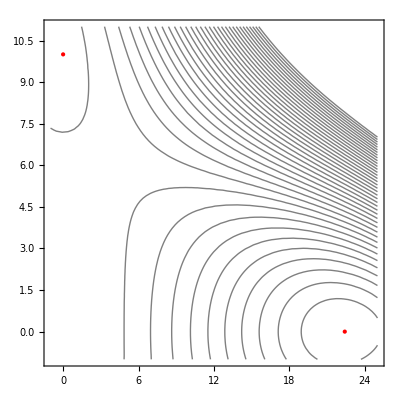
Show[-Graphics-,ParametricPlot[Through[bf[Bounce][r]],{r,rInit,rFin}]]

```mathematica
{rInit,rFin}=MinMax@bf["Radii"];
Show[ContourPlot[V[h,s],{h,-1,25},{s,-1,11},Contours->40,ContourShading->None,ContourStyle->Gray,Epilog->{PointSize[Large],Red,Point[minima]}],ParametricPlot[Through@bf["Bounce"][r],{r,rInit,rFin}]]
```

We can also plot the final bounce field configuration for both fields.

```mathematica
BouncePlot[bf,PlotLabel->Row[{"Action = ",bf["Action"]}],PlotStyle->{Purple,Orange}]
```

BouncePlot[bf,PlotLabel→Action = bf[Action],PlotStyle→{RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0]}]